```mathematica
f[b_, fi_]=(1 - Exp[-b*fi])/ (1 - Exp[-b]);
g[b_, x_] = -Log[1+(Exp[-b] - 1)*x] /b;
h[b_, fi_, e_] = g[b, f[b, 1 - fi] + e];
Solve[h[1, x, e] == x, x]
Solve[h[10, x, e] == x, x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→Log[1/2 (e (-1+ⅇ)-√(4 ⅇ+e^2 (1-2 ⅇ+ⅇ^2)))]},{x→Log[1/2 (e (-1+ⅇ)+√(4 ⅇ+e^2 (1-2 ⅇ+ⅇ^2)))]}}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→Log[-((-e+e ⅇ^10-√(e^2+4 ⅇ^10-2 e^2 ⅇ^10+e^2 ⅇ^20))^(1/10))/2^(1/10)]},{x→Log[((-e+e ⅇ^10-√(e^2+4 ⅇ^10-2 e^2 ⅇ^10+e^2 ⅇ^20))^(1/10))/2^(1/10)]},{x→Log[-((-1)^(1/5) (-e+e ⅇ^10-√(e^2+4 ⅇ^10-2 e^2 ⅇ^10+e^2 ⅇ^20))^(1/10))/2^(1/10)]},{x→Log[((-1)^(1/5) (-e+e ⅇ^10-√(e^2+4 ⅇ^10-2 e^2 ⅇ^10+e^2 ⅇ^20))^(1/10))/2^(1/10)]},{x→Log[-((-1)^(2/5) (-e+e ⅇ^10-√(e^2+4 ⅇ^10-2 e^2 ⅇ^10+e^2 ⅇ^20))^(1/10))/2^(1/10)]},{x→Log[((-1)^(2/5) (-e+e ⅇ^10-√(e^2+4 ⅇ^10-2 e^2 ⅇ^10+e^2 ⅇ^20))^(1/10))/2^(1/10)]},{x→Log[-((-1)^(3/5) (-e+e ⅇ^10-√(e^2+4 ⅇ^10-2 e^2 ⅇ^10+e^2 ⅇ^20))^(1/10))/2^(1/10)]},{x→Log[((-1)^(3/5) (-e+e ⅇ^10-√(e^2+4 ⅇ^10-2 e^2 ⅇ^10+e^2 ⅇ^20))^(1/10))/2^(1/10)]},{x→Log[-((-1)^(4/5) (-e+e ⅇ^10-√(e^2+4 ⅇ^10-2 e^2 ⅇ^10+e^2 ⅇ^20))^(1/10))/2^(1/10)]},{x→Log[((-1)^(4/5) (-e+e ⅇ^10-√(e^2+4 ⅇ^10-2 e^2 ⅇ^10+e^2 ⅇ^20))^(1/10))/2^(1/10)]},{x→Log[-((-e+e ⅇ^10+√(e^2+4 ⅇ^10-2 e^2 ⅇ^10+e^2 ⅇ^20))^(1/10))/2^(1/10)]},{x→Log[((-e+e ⅇ^10+√(e^2+4 ⅇ^10-2 e^2 ⅇ^10+e^2 ⅇ^20))^(1/10))/2^(1/10)]},{x→Log[-((-1)^(1/5) (-e+e ⅇ^10+√(e^2+4 ⅇ^10-2 e^2 ⅇ^10+e^2 ⅇ^20))^(1/10))/2^(1/10)]},{x→Log[((-1)^(1/5) (-e+e ⅇ^10+√(e^2+4 ⅇ^10-2 e^2 ⅇ^10+e^2 ⅇ^20))^(1/10))/2^(1/10)]},{x→Log[-((-1)^(2/5) (-e+e ⅇ^10+√(e^2+4 ⅇ^10-2 e^2 ⅇ^10+e^2 ⅇ^20))^(1/10))/2^(1/10)]},{x→Log[((-1)^(2/5) (-e+e ⅇ^10+√(e^2+4 ⅇ^10-2 e^2 ⅇ^10+e^2 ⅇ^20))^(1/10))/2^(1/10)]},{x→Log[-((-1)^(3/5) (-e+e ⅇ^10+√(e^2+4 ⅇ^10-2 e^2 ⅇ^10+e^2 ⅇ^20))^(1/10))/2^(1/10)]},{x→Log[((-1)^(3/5) (-e+e ⅇ^10+√(e^2+4 ⅇ^10-2 e^2 ⅇ^10+e^2 ⅇ^20))^(1/10))/2^(1/10)]},{x→Log[-((-1)^(4/5) (-e+e ⅇ^10+√(e^2+4 ⅇ^10-2 e^2 ⅇ^10+e^2 ⅇ^20))^(1/10))/2^(1/10)]},{x→Log[((-1)^(4/5) (-e+e ⅇ^10+√(e^2+4 ⅇ^10-2 e^2 ⅇ^10+e^2 ⅇ^20))^(1/10))/2^(1/10)]}}

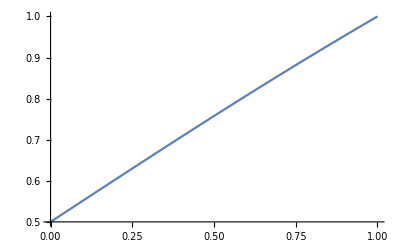

```mathematica
Plot[Log[1/2 ((-1+E) e+Sqrt[4 E+(1-2 E+E^2) e^2])],{e,0,1}]
```

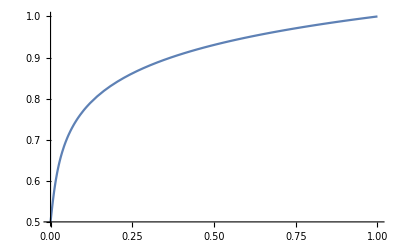

```mathematica
Plot[Log[-(-(-e+E^10 e+Sqrt[e^2+4 E^10-2 E^10 e^2+E^20 e^2])^(1/10)/2^(1/10))],{e,0,1}]
```